## Coupled VAE Analysis

### Input Maximum Likelihood Data

```mathematica
CVAEFolder = "/Users/kenricnelson/Documents/Wolfram Mathematica/Coupled VAE/Rcode/";
```

```mathematica
CoupledVAEData=Exp[Flatten[
Import[CVAEFolder<>"ml"<>#<>"_alpha2","CSV"]
]&/@{"0","025","005","01"}
]
```

{{4.0174479590083631×10^-32,2.6869914090653067×10^-38,3.828901172625566×10^-47,4995,1.4341824031247758×10^-39,1.197150742890112×10^-20},2,{37,4998,48}}
 |  |  |  |

### Define LikelihoodHistogram

```mathematica
Clear[LikelihoodHistogram,AccuracyPlot,AccuracyMetrics];
LikelihoodHistogram[x_]:=Module[{HistRange={0.35,1600 }},Show[
Histogram[x,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},HistRange},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold],
ChartElementFunction->"EdgeFadingRectangle"
],
AccuracyPlot[AccuracyMetrics[x]]
]];
AccuracyPlot[x_]:=Module[{HistRange={0.37,1600 }},ListLogLogPlot[{
Labeled[{x⟦1⟧,HistRange⟦2⟧-1500},"Robustness",Above],
Labeled[{x⟦2⟧,HistRange⟦2⟧-350},"Accuracy ", Above],
Labeled[{x⟦3⟧,HistRange⟦2⟧-1000}," Decisiveness",Above]
},
LabelStyle->Directive[Medium, Blend[{Blue,Gray},0.75],Bold],
Filling->HistRange⟦1⟧,
FillingStyle->Thick,
PlotMarkers->{Automatic,.1}
]];
AccuracyMetrics[x_]:=
WeightedGeneralizedMean[x,#]&/@{-3/2,0,1};
```

### Plots

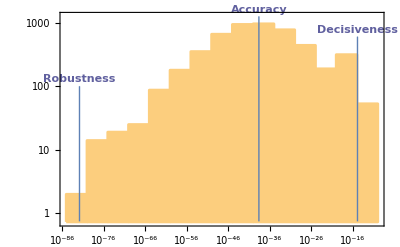

```mathematica
LikelihoodHistogram[CoupledVAEData⟦1,All⟧]
```

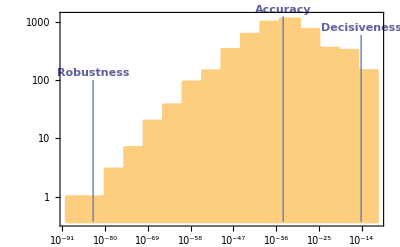

```mathematica
LikelihoodHistogram[CoupledVAEData⟦2,All⟧]
```

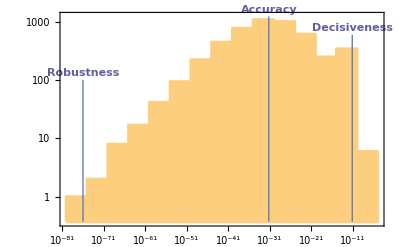

```mathematica
LikelihoodHistogram[CoupledVAEData⟦3,All⟧]
```

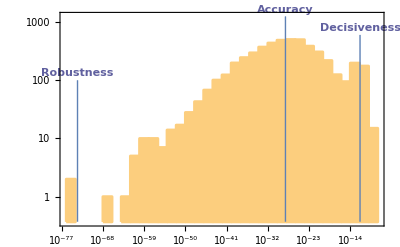

```mathematica
LikelihoodHistogram[CoupledVAEData⟦4,All⟧]
```

### Draft Functions

```mathematica
Clear[LikelihoodHistogram];
LikelihoodHistogram[x_]:=Show[
Histogram[x,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},{.7,1500}},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold],
ChartElementFunction->"EdgeFadingRectangle"
],
AccuracyPlot[AccuracyMetrics[x]]
];
AccuracyPlot[x_]:=ListLogLogPlot[{
Labeled[{x⟦1⟧,1000},"Robustness",Above],
Labeled[{x⟦2⟧,1000},"Accuracy", Above],
Labeled[{x⟦3⟧,1000},"Decisiveness",Above]
},
LabelStyle->Directive[Medium, Blend[{Blue,Gray},0.75],Bold],
Filling->0.75,
FillingStyle->Thick,
PlotMarkers->{Automatic,.1}
];
AccuracyMetrics[x_]:=
WeightedGeneralizedMean[x,#]&/@{-3/2,0,1};
```

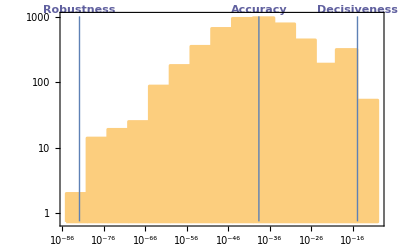

```mathematica
LikelihoodHistogram[LikelihoodKappa0Alpha2]
```

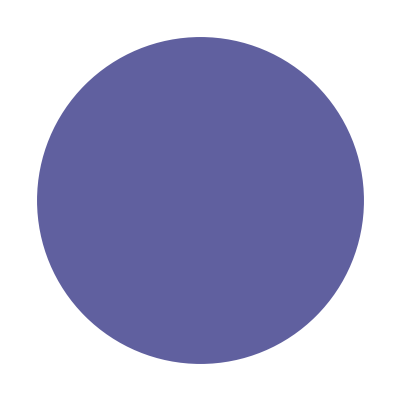

```mathematica
Graphics[{Blend[{Blue,Gray},0.75],Disk[]}]
```

```mathematica
SaveAccMet=AccuracyMetrics[LikelihoodKappa0Alpha2];
```

```mathematica
Clear[AccuracyPlot];
AccuracyPlot[x_]:=ListLogLogPlot[{
Labeled[{x⟦1⟧,1000},"Robustness",Right],
Labeled[{x⟦2⟧,1000},"Accuracy",Right],
Labeled[{x⟦3⟧,1000},"Decisiveness",Right]
},
LabelStyle->Directive[Medium, Bold],
Filling->Bottom,
FillingStyle->Thick,
PlotMarkers->{Automatic,.1}];
```

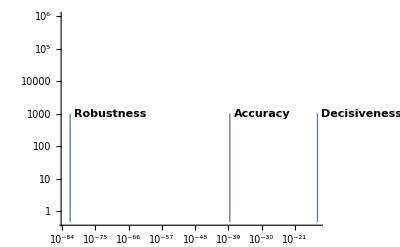

```mathematica
AccuracyPlot[SaveAccMet]
```

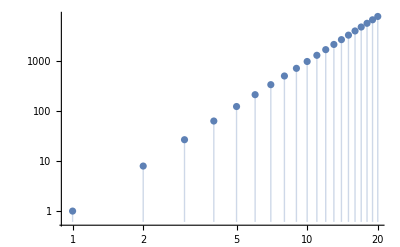

```mathematica
ListLogLogPlot[Range[20]^3,Filling->Bottom]
```

```mathematica
LikelihoodHistogram[x_]:=Histogram[x,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},{.7,1000}},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold]
];
AccuracyMetrics[x_]:=
WeightedGeneralizedMean[x,#]&/@{-3/2,0,1};
```

```mathematica
AccuracyPlot[x_]:=ListLinePlot[{
Labeled[{{x⟦1⟧,0.7},{x⟦1⟧,1000}},"Robustness"],
Labeled[{{x⟦2⟧,0.7},{x⟦2⟧,1000}},"Accuracy"],
Labeled[{{x⟦3⟧,0.7},{x⟦3⟧,1000}},"Decisiveness"]
}];
```

```mathematica
AccuracyPlot[AccuracyMetrics[LikelihoodKappa0Alpha2]]
```

-Graphics-

```mathematica
AccuracyMetrics[LikelihoodKappa0Alpha2]
```

{1.5598×10^-82,2.41385×10^-39,1.31033×10^-15}

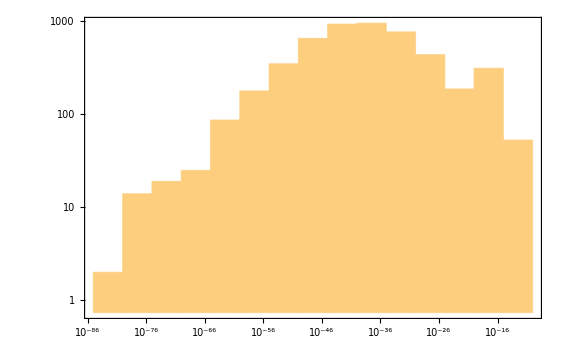

```mathematica
Histogram[LikelihoodKappa0Alpha2,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},{.7,1000}},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold]
]
```

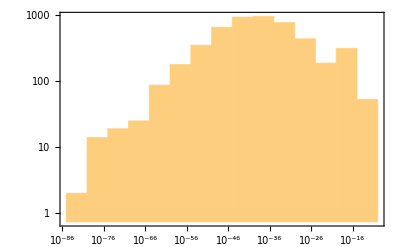

```mathematica
Show[%50,Axes->True,AxesStyle->Black]
```

```mathematica
Histogram[LikelihoodKappa0Alpha2,"Log",PlotTheme->"Detailed",ScalingFunctions->{"Log","Log"},PlotRange->{{1/100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,1/10000000000},{1,1000}},AxesOrigin->{1/10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,1/100000}]
```

-Graphics-

```mathematica
ChartElementData["Histogram"]
```

{ArrowRectangle,EdgeFadingRectangle,FadingRectangle,GlassRectangle,GradientRectangle,GradientScaleRectangle,ObliqueRectangle,Rectangle,SegmentScaleRectangle}

```mathematica
ChartElementData["BarChart"]
```

{ArrowRectangle,EdgeFadingRectangle,FadingRectangle,GlassRectangle,GradientRectangle,GradientScaleRectangle,ObliqueRectangle,Rectangle,SegmentScaleRectangle}

## Coupled Divergence for the VAE

```mathematica
$Assumptions={μPost,σPost,μPrior,σPrior,μPost1,μPost2,σPost1,σPost2,κ}∈Reals&&0<μPost<∞&&0<σPost<∞&&0<μPrior<∞&&0<σPost<∞&&0<κ<∞;
```

### One Dimensional Case

```mathematica
CoupledDivergence[NormalDistribution[μPost,σPost], NormalDistribution[μPrior,σPrior],κ]
```

-∫_(-∞)^∞ If[κ/(1+2 κ)==0,PDF[NormalDistribution[μPost,σPost],x],FullSimplify[PDF[NormalDistribution[μPost,σPost],x]^(1--κ/(1+2 κ))/(∫_(-∞)^∞ PDF[NormalDistribution[μPost,σPost],y]^(1--κ/(1+2 κ))ⅆy)]] If[ⅇ^((x-μPost)^2/(2 σPost^2)) σPost≥0,If[κ≠0,((ⅇ^((x-μPost)^2/(2 σPost^2)) √(2 π) σPost)^(κ/(1+2 κ))-1)/κ,Log[ⅇ^((x-μPost)^2/(2 σPost^2)) √(2 π) σPost]],Undefined]ⅆx+∫_(-∞)^∞ 1/2 If[κ/(1+κ)==0,PDF[NormalDistribution[μPost,σPost],x],FullSimplify[PDF[NormalDistribution[μPost,σPost],x]^(1--(2 κ)/(1+κ))/(∫_(-∞)^∞ PDF[NormalDistribution[μPost,σPost],y]^(1--(2 κ)/(1+κ))ⅆy)]] If[ⅇ^((x-μPrior)^2/σPrior^2) σPrior^2≥0,If[κ≠0,((2 ⅇ^((x-μPrior)^2/σPrior^2) π σPrior^2)^(κ/(1+1 κ))-1)/κ,Log[2 ⅇ^((x-μPrior)^2/σPrior^2) π σPrior^2]],Undefined]ⅆx

```mathematica
-∫_(-∞)^∞ FullSimplify[PDF[NormalDistribution[μPost,σPost],x]^(1--κ/(1+2 κ))/(∫_(-∞)^∞ PDF[NormalDistribution[μPost,σPost],y]^(1--κ/(1+2 κ))ⅆy)]((ⅇ^((x-μPost)^2/(2 σPost^2)) √(2 π) σPost)^(κ/(1+2 κ))-1)/κ ⅆx+∫_(-∞)^∞ 1/2 FullSimplify[PDF[NormalDistribution[μPost,σPost],x]^(1--(2 κ)/(1+κ))/(∫_(-∞)^∞ PDF[NormalDistribution[μPost,σPost],y]^(1--(2 κ)/(1+κ))ⅆy)]((2 ⅇ^((x-μPrior)^2/σPrior^2) π σPrior^2)^(κ/(1+1 κ))-1)/κ ⅆx
```

```mathematica
1/κ-((2 π)^(κ/(2+4 κ)) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(κ+2 κ^2)+1/(4 κ)(-3+(2^(1+κ/(1+κ)) ⅇ^(-(κ (1+3 κ) (μPost-μPrior)^2)/((1+κ) (2 κ σPost^2-σPrior^2-3 κ σPrior^2))) π^(κ/(1+κ)) σPrior^2 Abs[σPrior]^((-1+κ)/(1+κ)))/(√((-2 κ σPost^2+σPrior^2+3 κ σPrior^2)/(1+3 κ)))+Erf[(√((1+3 κ)/(1+κ)) μPost)/(√2 σPost)]+GammaRegularized[1/2,((1+3 κ) μPost^2)/(2 (1+κ) σPost^2)])//FullSimplify
```

$Aborted

Set μPrior to zero since this expression is very complex

```mathematica
1/κ-((2 π)^(κ/(2+4 κ)) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(κ+2 κ^2)+1/(4 κ)(-3+(2^(1+κ/(1+κ)) ⅇ^(-(κ (1+3 κ) (μPost-μPrior)^2)/((1+κ) (2 κ σPost^2-σPrior^2-3 κ σPrior^2))) π^(κ/(1+κ)) σPrior^2 Abs[σPrior]^((-1+κ)/(1+κ)))/(√((-2 κ σPost^2+σPrior^2+3 κ σPrior^2)/(1+3 κ)))+Erf[(√((1+3 κ)/(1+κ)) μPost)/(√2 σPost)]+GammaRegularized[1/2,((1+3 κ) μPost^2)/(2 (1+κ) σPost^2)])/.μPrior->0//FullSimplify
```

1/κ-((2 π)^(κ/(2+4 κ)) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(κ+2 κ^2)+(-1+(ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (-2 κ σPost^2+σPrior^2+3 κ σPrior^2))) (2 π)^(κ/(1+κ)) Abs[σPrior]^(3-2/(1+κ)))/(√(-(2 κ σPost^2)/(1+3 κ)+σPrior^2)))/(2 κ)

```mathematica
FullSimplify[1/κ-((2 π)^(κ/(2+4 κ)) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(κ+2 κ^2)+(-1+(ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (-2 κ σPost^2+σPrior^2+3 κ σPrior^2))) (2 π)^(κ/(1+κ)) Abs[σPrior]^(3-2/(1+κ)))/(√(-(2 κ σPost^2)/(1+3 κ)+σPrior^2)))/(2 κ)]
```

1/κ-((2 π)^(κ/(2+4 κ)) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(κ+2 κ^2)+(-1+(ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (-2 κ σPost^2+σPrior^2+3 κ σPrior^2))) (2 π)^(κ/(1+κ)) Abs[σPrior]^(3-2/(1+κ)))/(√(-(2 κ σPost^2)/(1+3 κ)+σPrior^2)))/(2 κ)

Simplify by hand

```mathematica
1/(2κ)-1/κ(2 π)^(κ/(2+4 κ)) √((1+3 κ)/(1+2κ)) σPost^(κ/(1+2 κ))+(2 π)^(κ/(1+κ))ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (-2 κ σPost^2+σPrior^2+3 κ σPrior^2)))  √((1+3κ)/(-2 κ σPost^2+(1+3κ)σPrior^2))σPrior^((3+κ)/(1+κ))
```

Check the case when σPrior = 1

```mathematica
1/κ-((2 π)^(κ/(2+4 κ)) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(κ+2 κ^2)+(-1+(ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (-2 κ σPost^2+σPrior^2+3 κ σPrior^2))) (2 π)^(κ/(1+κ)) Abs[σPrior]^(3-2/(1+κ)))/(√(-(2 κ σPost^2)/(1+3 κ)+σPrior^2)))/(2 κ)/.σPrior->1//FullSimplify
```

1/κ-((2 π)^(κ/(2+4 κ)) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(κ+2 κ^2)+(-1+(ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (1+κ (3-2 σPost^2)))) (2 π)^(κ/(1+κ)))/(√(1-(2 κ σPost^2)/(1+3 κ))))/(2 κ)

Simplify by hand

```mathematica
(2 π)^(κ/(1+κ))/(2κ)((2 π)^(-κ/(1+κ))-(2(2 π)^(-(κ (1+3 κ))/(2(1+2κ)(1+κ))) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(1+2 κ)+ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (1+κ (3-2 σPost^2))))√((1+3 κ)/(1+3 κ-2 κ σPost^2)) )
```

#### Comparison with Shichen Cao’s Python Code

d1 = 1 + d * k + 2 * k
 KL_d1 = tf.reduce_prod(tf.pow(2 * tf.constant(m.pi), k / (1 + d * k)) * tf.sqrt(d1 / (d1 - 2 * k * tf.square(stddev)))
                           * tf.exp(tf.square(mean) * d1 * k / (1 + d * k) / (d1 - 2 * k * tf.square(stddev))), 1)
 KL_d2 = tf.reduce_prod(tf.pow(2 * tf.constant(m.pi) * tf.square(stddev),
                                  k / (1 + k * d)) * tf.sqrt(d1 / (1 + d * k)), 1)
 KL_divergence = (KL_d1 - KL_d2) / k / 2

```mathematica
KLTerm1 = (2π)^(κ/(1+κ))√((1+3κ)/(1+3κ-2κ σPost^2))Exp[μPost^2((1+3κ)κ)/((1+κ)(1+3κ-2κ σPost^2))];
KLTerm2=(2π σPost^2)^(κ/(1+κ))√((1+3κ)/(1+κ));
```

```mathematica
KLDivergence =(KLTerm1-KLTerm2)/(2κ)//FullSimplify
```

(2^(-1/(1+κ)) π^(κ/(1+κ)) (-√(3-2/(1+κ)) (σPost^2)^(κ/(1+κ))+ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (1+κ (3-2 σPost^2)))) √((1+3 κ)/(1+3 κ-2 κ σPost^2))))/κ

```mathematica
((2π)^(κ/(1+κ)) (-√(3-2/(1+κ)) (σPost^2)^(κ/(1+κ))+ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (1+κ (3-2 σPost^2)))) √((1+3 κ)/(1+3 κ-2 κ σPost^2))))/(2κ)
```

Determine whether new derivation equals Cao’s code
* From inspection, the multiplying term (2 π)^(κ/(1+κ))/(2κ)and the second additive term ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (1+κ (3-2 σPost^2)))) √((1+3 κ)/(1+3 κ-2 κ σPost^2))are equal.  Need to determine whether the first additive terms are equal

```mathematica
(2 π)^(-κ/(1+κ))-(2(2 π)^(-(κ (1+3 κ))/(2(1+2κ)(1+κ))) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(1+2 κ)==-√(3-2/(1+κ)) (σPost^2)^(κ/(1+κ))
```

(2 π)^(-κ/(1+κ))-(2^(1-(κ (1+3 κ))/(2 (1+κ) (1+2 κ))) π^(-(κ (1+3 κ))/(2 (1+κ) (1+2 κ))) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(1+2 κ)==-√(3-2/(1+κ)) (σPost^2)^(κ/(1+κ))

```mathematica
(2 π)^(-κ/(1+κ))-(2(2 π)^(-(κ (1+3 κ))/(2(1+2κ)(1+κ))) √(1+5 κ+6 κ^2) σPost^(κ/(1+2 κ)))/(1+2 κ)//FullSimplify
```

(2 π)^(-1+1/(1+κ))-(2^((2+5 κ+κ^2)/(2+6 κ+4 κ^2)) π^(-(κ (1+3 κ))/(2+6 κ+4 κ^2)) √(1+κ (5+6 κ)) σPost^(κ/(1+2 κ)))/(1+2 κ)

### Two Dimensional Case

```mathematica
CoupledDivergence[MultinormalDistribution[{μPost1,μPost2},{{σPost1,0},{0,σPost2}}], MultinormalDistribution[μPrior,σPrior],κ]
```